## Slot #

```mathematica
Array[Plus[##] &, {2, 2}]
```

{{2,3},{3,4}}

```mathematica
Array[Plus[#1,#2] &, {2, 2}]
```

{{2,3},{3,4}}

```mathematica
Array[Plus[##,#2] &, {2, 2}]
```

{{3,5},{4,6}}

```mathematica
Array[Plus[## #2] &, {2,2}]
```

{{1,4},{2,8}}

```mathematica
Plus[{2,2} 2]
```

{4,4}

## Plotting

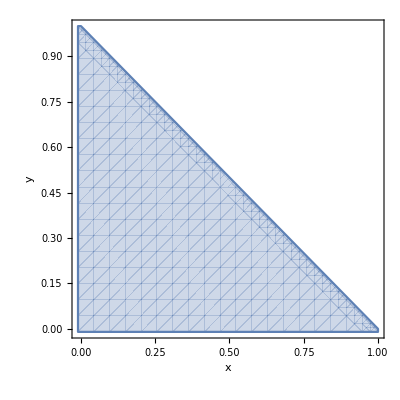

-Graphics3D-

```mathematica
RegionPlot[y<=1-x, {x,-.01,1},{y,-.01,1}, Axes:>True, AxesLabel->{x,y}]
RegionPlot3D[z<=1-x-y, {x,0,1},{y,0,1},{z,0,1}, AxesLabel->Automatic]
```

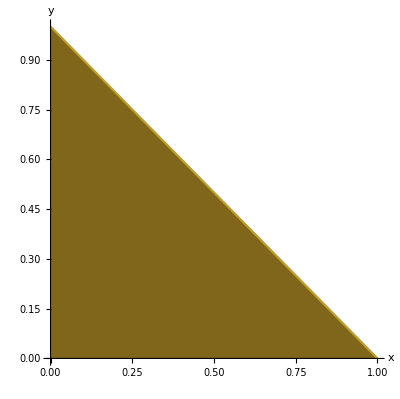

-Graphics3D-

```mathematica
Plot[1-x, {x, 0, 1}, Filling -> Bottom, AxesLabel->{x,y}, AspectRatio->Automatic] 
Plot3D[1-x-y, {x, 0, 1},{y, 0, 1}, 
RegionFunction->Function[{x,y,z}, 0<=z<=1], 
PlotStyle->Directive[Opacity[0.5,Blue]],
Filling -> Bottom, 
FillingStyle->Directive[Opacity[0.1,Blue]],
(* Mesh:>None, *) (* The mesh on the surface can be turned off *)
BoxRatios:>{1,1,1}, 
AxesLabel->{Subscript[x,1],Subscript[x,2],Subscript[x,3]},
BoundaryStyle->Directive[Red, Thick]]
```

## Dual basis vectors

```mathematica
vec = {r*Sin[θ]*Cos[ϕ], r*Sin[θ]*Sin[ϕ], r*Cos[θ] }
rmag = Simplify[Norm[vec], Assumptions->{r>0,θ∈Reals,ϕ∈Reals}]
```

{r Cos[ϕ] Sin[θ],r Sin[θ] Sin[ϕ],r Cos[θ]}

r

```mathematica
pars = {{r, Sqrt[x^2+y^2+z^2]},
		{θ, ArcCos[z/Sqrt[x^2+y^2+z^2]]},
		{ϕ, ArcTan[y/x]}
		}
coords = {
x:> r*Sin[θ]*Cos[ϕ],
y:> r*Sin[θ]*Sin[ϕ],
z:> r*Cos[θ]
}
```

{{r,√(x^2+y^2+z^2)},{θ,ArcCos[z/(√(x^2+y^2+z^2))]},{ϕ,ArcTan[y/x]}}

{x:>r Sin[θ] Cos[ϕ],y:>r Sin[θ] Sin[ϕ],z:>r Cos[θ]}

```mathematica
e[x_] := D[vec, pars[[x,1]] ]
Do[Print[Subscript[Style[e,Bold], pars[[i,1]]], " = ", e[i]], {i,1,3}]
```

e_r = {Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}

e_θ = {r Cos[θ] Cos[ϕ],r Cos[θ] Sin[ϕ],-r Sin[θ]}

e_ϕ = {-r Sin[θ] Sin[ϕ],r Cos[ϕ] Sin[θ],0}

```mathematica
g = Table[e[i].e[j], {i, 3}, {j, 3}] // Simplify ;
g // MatrixForm
```

(1 | 0 | 0
0 | r^2 | 0
0 | 0 | r^2 Sin[θ]^2)

```mathematica
f[a_] := Simplify[∇_{x,y,z} pars[[a,2]] /. coords,
				  Assumptions->{r>0,0<θ<Pi,ϕ∈Reals}
				  ] 
Do[Print[Style[e,Bold]^pars[[i,1]]," = ",f[i]], {i,1,3}]
```

e^r = {Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}

e^θ = {(Cos[θ] Cos[ϕ])/r,(Cos[θ] Sin[ϕ])/r,-Sin[θ]/r}

e^ϕ = {-(Csc[θ] Sin[ϕ])/r,(Cos[ϕ] Csc[θ])/r,0}

```mathematica
check[i_] := Sum[ g[[i,j]]*f[j], {j,1,Length[g]} ] (* contract g_ij * e^j *)
Do[ Print[Subscript["e", pars[[i,1]]],(" = e")^pars[[i,1]]," ---> " ,check[i]===e[i]], {i,1,Length[g]} ]
```

e_r(= e)^r ---> True

e_θ(= e)^θ ---> True

e_ϕ(= e)^ϕ ---> True

## Tree form

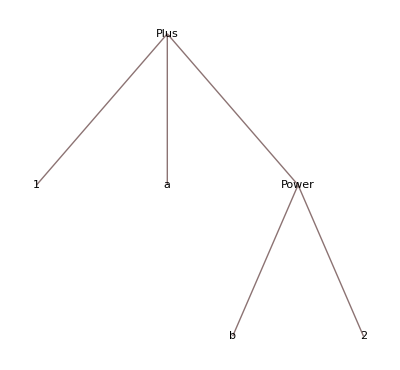

```mathematica
TreeForm[1+a+b^2]
```

SetDelayed::write: Tag List in {{1,0,0},{0,r^2,0},{0,0,r^2 Sin[θ]^2}}[a_] is Protected.

$Failed

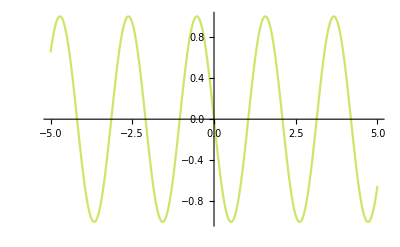

```mathematica
f[a_] := Sin[a(2*Pi-x)] 
g[a_] := Sin[-a*x]
Plot[{f[3], g[3]}, {x,-5,5}]
```

## Sound

```mathematica
EmitSound[Sound[SoundNote[{"Snare", "BassDrum"}]]]
Pause[0.08]
EmitSound[Sound[SoundNote["Snare"]]]
Pause[0.4]
Do[{EmitSound[Sound[SoundNote[{"RideCymbal", "Snare", "BassDrum2"}]]], 
Pause[0.04],
EmitSound[Sound[SoundNote["BassDrum"]]]
}, {20}]
Pause[1/2]
EmitSound[Sound[SoundNote[{"CrashCymbal", "BassDrum2"}]]]
```

## Inverting a system

```mathematica
SetDirectory[NotebookDirectory[]]
<< "result.txt";
data = %[[1,2,1;;3]]
```

/home/jkrys/Desktop/Level 4/Project/Mathematica

Get::noopen: Cannot open result.txt.

Part::partd: Part specification $Failed⟦1,2,1;;3⟧ is longer than depth of object.

$Failed⟦1,2,1;;3⟧

```mathematica
xs = Transpose[data][[1]]
ys = Transpose[data][[2]]
data
coeffs = NSolve[
		{a/(xs[[1]]^2) + b/xs[[1]] + c == ys[[1]], 
         a/(xs[[2]]^2) + b/xs[[2]] + c == ys[[2]],
         a/(xs[[3]]^2) + b/xs[[3]] + c == ys[[3]]
        }, 
	{a,b,c}
	];
	
Plot[a/(x^2) + b/x + c /. coeffs, {x,-0.2, 0}]
```

$Failed⟦1,2,1;;3⟧

Part::partw: Part 2 of Transpose[$Failed⟦1,2,1;;3⟧] does not exist.

Transpose[$Failed⟦1,2,1;;3⟧]⟦2⟧

$Failed⟦1,2,1;;3⟧

Part::partw: Part 3 of Transpose[$Failed⟦1,2,1;;3⟧]⟦2⟧ does not exist.

-Graphics-

## Numerical errors

```mathematica
f[x_] := 1/π Cos[80 Sin[x] - x];

res = NIntegrate[f[x], {x, 0, 2Pi}, 
  Method -> {"Trapezoidal", "SymbolicProcessing" -> 0},
  IntegrationMonitor :> ((errors = Through[#1@"Error"]) &)];

res
Length[errors]
Total[errors]

(* 
  -0.112115          <-- integral value
  2.67841*10^-15     <-- error estimate by NIntegrate
  4.996*10^-16       <-- actual error
*)
```

-0.112115

1

2.67841×10^-15

```mathematica
f[x_] := 1/π Cos[80 Sin[x] - x];

res2[a_] := NIntegrate[f[x], {x, 0, a*Pi},
 PrecisionGoal -> 7,
 IntegrationMonitor :> ((errors = Through[#1@"Error"]) &)]
res2[2]
errors;
Length[errors]
Total[errors] (* sums the errors for all subregions *)
(*
  -0.112115          <-- integral value
  175                <-- length of errors = number of subregions
  1.1067647*10^-8    <-- overall error estimate
*)
```

-0.112115

149

1.10676×10^-8

```mathematica
numvalues[{s12_,s23_}] := Module[{x,y,i},
x = ConstantArray[0, {Length[epslist], 2} ] ;
Do[x[[i]] = {epslist[[i]], res[s12,s23,epslist[[i]]]}, {i,1,Length[epslist]}];
{{s12, s23}, x}
]

num = Map[numvalues, points]
num[[1,2,1,2]]
```

points

Part::partd: Part specification points⟦1,2,1,2⟧ is longer than depth of object.

points⟦1,2,1,2⟧

```mathematica
f[x_] := 1/π Cos[80 Sin[x] - x];

iRegionMethods = {"Axis", "Boundaries", "Dimension", "Error", 
  "GetRule", "Integral", "Integrand", "WorkingPrecision"}; 
 
res = Reap@NIntegrate[f[x], {x, 0, Pi}, PrecisionGoal -> 1.1, 
   Method -> "AdaptiveMonteCarlo", 
   IntegrationMonitor :> 
    Function[{iregs}, 
     Sow[Association /@ 
       Transpose[
        Map[Thread[# -> Through[iregs[#]]] &, iRegionMethods]]]]];
Dataset[Flatten[res[[2]]]]
```

Dataset[<>]

```mathematica
numericalint00[ϵ_,s12_,s23_] :=
        (Gamma[1 - 2 ϵ] Gamma[
        2 + ϵ] (1/(-s23 x z +
        s12 y (-1 + x + y + z)))^(2 + ϵ))/(
        Gamma[1 - ϵ]^2 Gamma[1 + ϵ])

cut = 10^(-10)

numericalint[ϵ_,s12_,s23_] :=  NIntegrate[numericalint00[ϵ,s12,s23], {x,cut,1-cut}, {y,cut,1-cut-x}, {z,cut,1-cut-x-y},
MinRecursion->10^5, MaxRecursion->10^12,
Method -> {"GlobalAdaptive", "MaxErrorIncreases" ->10^4},
PrecisionGoal->4,
WorkingPrecision->20,
IntegrationMonitor :> ((errors = Through[#1@"Error"]) &)]

res = numericalint[-1/20,-3,-1]
err = Total[errors]
Print[res]
Print[err]
SetDirectory[NotebookDirectory[]]
Save["test.txt", {res,err}]
```

1/10000000000

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

0.733233581161122697308

{-0.0532372,{{{<|Axis→1,Boundaries→{{0,1}},Dimension→1,Error→0.0700002,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0154151,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0,0.6}},Dimension→1,Error→0.0409547,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0918237,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6,1}},Dimension→1,Error→0.0257888,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0110755,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0.6,1}},Dimension→1,Error→0.0257888,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0110755,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0,0.36}},Dimension→1,Error→0.0243792,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00536078,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.36,0.6}},Dimension→1,Error→0.0186326,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0469444,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0,0.36}},Dimension→1,Error→0.0243792,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00536078,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.36,0.6}},Dimension→1,Error→0.0186326,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0469444,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6,0.84}},Dimension→1,Error→0.0168306,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0197453,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.84,1}},Dimension→1,Error→0.0108919,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0109399,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0.36,0.6}},Dimension→1,Error→0.0186326,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0469444,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6,0.84}},Dimension→1,Error→0.0168306,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0197453,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.84,1}},Dimension→1,Error→0.0108919,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0109399,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0,0.216}},Dimension→1,Error→0.0155035,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.000665902,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.216,0.36}},Dimension→1,Error→0.0100266,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0136089,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0.6,0.84}},Dimension→1,Error→0.0168306,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0197453,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0,0.216}},Dimension→1,Error→0.0155035,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.000665902,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.216,0.36}},Dimension→1,Error→0.0100266,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0136089,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.36,0.504}},Dimension→1,Error→0.00917918,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0569039,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.84,1}},Dimension→1,Error→0.0108919,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0109399,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.504,0.6}},Dimension→1,Error→0.00719306,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0109064,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0,0.216}},Dimension→1,Error→0.0155035,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.000665902,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.84,1}},Dimension→1,Error→0.0108919,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0109399,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.504,0.6}},Dimension→1,Error→0.00719306,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0109064,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.36,0.504}},Dimension→1,Error→0.00917918,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0569039,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.216,0.36}},Dimension→1,Error→0.0100266,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0136089,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6,0.744}},Dimension→1,Error→0.00989083,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00100091,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.744,0.84}},Dimension→1,Error→0.00655189,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00199227,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0.84,1}},Dimension→1,Error→0.0108919,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0109399,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.216,0.36}},Dimension→1,Error→0.0100266,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0136089,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6,0.744}},Dimension→1,Error→0.00989083,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00100091,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.36,0.504}},Dimension→1,Error→0.00917918,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0569039,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.744,0.84}},Dimension→1,Error→0.00655189,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00199227,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0,0.1296}},Dimension→1,Error→0.00931737,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0105274,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.504,0.6}},Dimension→1,Error→0.00719306,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0109064,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.1296,0.216}},Dimension→1,Error→0.00584338,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00017289,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0.216,0.36}},Dimension→1,Error→0.0100266,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0136089,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0,0.1296}},Dimension→1,Error→0.00931737,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0105274,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.36,0.504}},Dimension→1,Error→0.00917918,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0569039,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.744,0.84}},Dimension→1,Error→0.00655189,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00199227,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.1296,0.216}},Dimension→1,Error→0.00584338,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00017289,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.504,0.6}},Dimension→1,Error→0.00719306,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0109064,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6,0.744}},Dimension→1,Error→0.00989083,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00100091,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.84,0.904}},Dimension→1,Error→0.00430185,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0134969,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.904,1}},Dimension→1,Error→0.00660691,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00498996,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0.6,0.744}},Dimension→1,Error→0.00989083,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00100091,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0,0.1296}},Dimension→1,Error→0.00931737,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0105274,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.36,0.504}},Dimension→1,Error→0.00917918,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0569039,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.744,0.84}},Dimension→1,Error→0.00655189,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00199227,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.1296,0.216}},Dimension→1,Error→0.00584338,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00017289,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.504,0.6}},Dimension→1,Error→0.00719306,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0109064,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.904,1}},Dimension→1,Error→0.00660691,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00498996,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.2736,0.36}},Dimension→1,Error→0.00592965,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00773228,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.216,0.2736}},Dimension→1,Error→0.00435809,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00229939,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.84,0.904}},Dimension→1,Error→0.00430185,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0134969,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0,0.1296}},Dimension→1,Error→0.00931737,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0105274,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.36,0.504}},Dimension→1,Error→0.00917918,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0569039,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.744,0.84}},Dimension→1,Error→0.00655189,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00199227,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.1296,0.216}},Dimension→1,Error→0.00584338,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00017289,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.504,0.6}},Dimension→1,Error→0.00719306,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0109064,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.2736,0.36}},Dimension→1,Error→0.00592965,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00773228,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.216,0.2736}},Dimension→1,Error→0.00435809,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00229939,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.84,0.904}},Dimension→1,Error→0.00430185,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0134969,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6,0.6864}},Dimension→1,Error→0.00536267,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0158363,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.904,1}},Dimension→1,Error→0.00660691,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00498996,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6864,0.744}},Dimension→1,Error→0.00409248,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00912489,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0.36,0.504}},Dimension→1,Error→0.00917918,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0569039,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.504,0.6}},Dimension→1,Error→0.00719306,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0109064,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.2736,0.36}},Dimension→1,Error→0.00592965,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00773228,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.216,0.2736}},Dimension→1,Error→0.00435809,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00229939,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.84,0.904}},Dimension→1,Error→0.00430185,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0134969,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6,0.6864}},Dimension→1,Error→0.00536267,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0158363,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.904,1}},Dimension→1,Error→0.00660691,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00498996,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6864,0.744}},Dimension→1,Error→0.00409248,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00912489,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.1296,0.216}},Dimension→1,Error→0.00584338,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00017289,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.744,0.84}},Dimension→1,Error→0.00655189,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00199227,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0,0.07776}},Dimension→1,Error→0.00530495,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00599649,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.07776,0.1296}},Dimension→1,Error→0.00356108,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00204437,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0.504,0.6}},Dimension→1,Error→0.00719306,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0109064,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.904,1}},Dimension→1,Error→0.00660691,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00498996,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.744,0.84}},Dimension→1,Error→0.00655189,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00199227,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0,0.07776}},Dimension→1,Error→0.00530495,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00599649,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.1296,0.216}},Dimension→1,Error→0.00584338,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00017289,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.07776,0.1296}},Dimension→1,Error→0.00356108,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00204437,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.36,0.4464}},Dimension→1,Error→0.0059239,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00358,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6864,0.744}},Dimension→1,Error→0.00409248,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00912489,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.4464,0.504}},Dimension→1,Error→0.000666677,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0526877,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.2736,0.36}},Dimension→1,Error→0.00592965,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00773228,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.216,0.2736}},Dimension→1,Error→0.00435809,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00229939,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.84,0.904}},Dimension→1,Error→0.00430185,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0134969,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6,0.6864}},Dimension→1,Error→0.00536267,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0158363,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0.904,1}},Dimension→1,Error→0.00660691,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00498996,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.2736,0.36}},Dimension→1,Error→0.00592965,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00773228,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.36,0.4464}},Dimension→1,Error→0.0059239,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00358,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6864,0.744}},Dimension→1,Error→0.00409248,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00912489,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6,0.6864}},Dimension→1,Error→0.00536267,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0158363,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.4464,0.504}},Dimension→1,Error→0.000666677,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0526877,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.216,0.2736}},Dimension→1,Error→0.00435809,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00229939,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.84,0.904}},Dimension→1,Error→0.00430185,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0134969,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.504,0.5424}},Dimension→1,Error→0.000458664,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0333456,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.744,0.84}},Dimension→1,Error→0.00655189,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00199227,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.1296,0.216}},Dimension→1,Error→0.00584338,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00017289,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.07776,0.1296}},Dimension→1,Error→0.00356108,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00204437,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.5424,0.6}},Dimension→1,Error→0.00312329,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0228212,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0,0.07776}},Dimension→1,Error→0.00530495,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00599649,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0.744,0.84}},Dimension→1,Error→0.00655189,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00199227,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.2736,0.36}},Dimension→1,Error→0.00592965,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00773228,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.36,0.4464}},Dimension→1,Error→0.0059239,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00358,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6864,0.744}},Dimension→1,Error→0.00409248,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00912489,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6,0.6864}},Dimension→1,Error→0.00536267,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0158363,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.4464,0.504}},Dimension→1,Error→0.000666677,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0526877,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0,0.07776}},Dimension→1,Error→0.00530495,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00599649,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.216,0.2736}},Dimension→1,Error→0.00435809,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00229939,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.84,0.904}},Dimension→1,Error→0.00430185,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0134969,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.504,0.5424}},Dimension→1,Error→0.000458664,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0333456,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.904,0.9424}},Dimension→1,Error→0.00237126,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0139532,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.1296,0.216}},Dimension→1,Error→0.00584338,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00017289,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.07776,0.1296}},Dimension→1,Error→0.00356108,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00204437,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.9424,1}},Dimension→1,Error→0.00394052,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00579344,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.5424,0.6}},Dimension→1,Error→0.00312329,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0228212,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0.2736,0.36}},Dimension→1,Error→0.00592965,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00773228,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.36,0.4464}},Dimension→1,Error→0.0059239,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00358,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6864,0.744}},Dimension→1,Error→0.00409248,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00912489,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6,0.6864}},Dimension→1,Error→0.00536267,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0158363,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.4464,0.504}},Dimension→1,Error→0.000666677,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0526877,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.1296,0.216}},Dimension→1,Error→0.00584338,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00017289,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0,0.07776}},Dimension→1,Error→0.00530495,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00599649,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.216,0.2736}},Dimension→1,Error→0.00435809,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00229939,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.84,0.904}},Dimension→1,Error→0.00430185,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0134969,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.504,0.5424}},Dimension→1,Error→0.000458664,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0333456,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.9424,1}},Dimension→1,Error→0.00394052,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00579344,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.5424,0.6}},Dimension→1,Error→0.00312329,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0228212,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.904,0.9424}},Dimension→1,Error→0.00237126,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0139532,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.7824,0.84}},Dimension→1,Error→0.0043535,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00365934,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.07776,0.1296}},Dimension→1,Error→0.00356108,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00204437,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.744,0.7824}},Dimension→1,Error→0.00251244,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00136533,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0.36,0.4464}},Dimension→1,Error→0.0059239,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00358,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.1296,0.216}},Dimension→1,Error→0.00584338,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00017289,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0,0.07776}},Dimension→1,Error→0.00530495,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00599649,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.216,0.2736}},Dimension→1,Error→0.00435809,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00229939,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.84,0.904}},Dimension→1,Error→0.00430185,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0134969,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.504,0.5424}},Dimension→1,Error→0.000458664,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0333456,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.9424,1}},Dimension→1,Error→0.00394052,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00579344,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.5424,0.6}},Dimension→1,Error→0.00312329,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0228212,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.904,0.9424}},Dimension→1,Error→0.00237126,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0139532,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6,0.6864}},Dimension→1,Error→0.00536267,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0158363,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.4464,0.504}},Dimension→1,Error→0.000666677,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0526877,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.7824,0.84}},Dimension→1,Error→0.0043535,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00365934,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.07776,0.1296}},Dimension→1,Error→0.00356108,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00204437,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.744,0.7824}},Dimension→1,Error→0.00251244,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00136533,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6864,0.744}},Dimension→1,Error→0.00409248,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00912489,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.2736,0.30816}},Dimension→1,Error→0.00239604,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00572948,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.30816,0.36}},Dimension→1,Error→0.00369605,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00460451,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0.1296,0.216}},Dimension→1,Error→0.00584338,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00017289,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0,0.07776}},Dimension→1,Error→0.00530495,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00599649,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.216,0.2736}},Dimension→1,Error→0.00435809,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00229939,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.84,0.904}},Dimension→1,Error→0.00430185,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0134969,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.504,0.5424}},Dimension→1,Error→0.000458664,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0333456,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.9424,1}},Dimension→1,Error→0.00394052,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00579344,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.5424,0.6}},Dimension→1,Error→0.00312329,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0228212,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.904,0.9424}},Dimension→1,Error→0.00237126,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0139532,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6,0.6864}},Dimension→1,Error→0.00536267,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0158363,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.7824,0.84}},Dimension→1,Error→0.0043535,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00365934,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6864,0.744}},Dimension→1,Error→0.00409248,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00912489,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.2736,0.30816}},Dimension→1,Error→0.00239604,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00572948,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.30816,0.36}},Dimension→1,Error→0.00369605,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00460451,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.07776,0.1296}},Dimension→1,Error→0.00356108,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00204437,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.744,0.7824}},Dimension→1,Error→0.00251244,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00136533,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.36,0.41184}},Dimension→1,Error→0.00405312,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00176325,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.4464,0.504}},Dimension→1,Error→0.000666677,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0526877,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.41184,0.4464}},Dimension→1,Error→0.00152364,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00951587,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0.6,0.6864}},Dimension→1,Error→0.00536267,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0158363,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0,0.07776}},Dimension→1,Error→0.00530495,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00599649,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.216,0.2736}},Dimension→1,Error→0.00435809,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00229939,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.84,0.904}},Dimension→1,Error→0.00430185,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0134969,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.504,0.5424}},Dimension→1,Error→0.000458664,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0333456,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.36,0.41184}},Dimension→1,Error→0.00405312,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00176325,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.9424,1}},Dimension→1,Error→0.00394052,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00579344,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.5424,0.6}},Dimension→1,Error→0.00312329,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0228212,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.904,0.9424}},Dimension→1,Error→0.00237126,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0139532,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.41184,0.4464}},Dimension→1,Error→0.00152364,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00951587,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.4464,0.504}},Dimension→1,Error→0.000666677,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0526877,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.7824,0.84}},Dimension→1,Error→0.0043535,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00365934,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6864,0.744}},Dimension→1,Error→0.00409248,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00912489,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.2736,0.30816}},Dimension→1,Error→0.00239604,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00572948,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.30816,0.36}},Dimension→1,Error→0.00369605,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00460451,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.07776,0.1296}},Dimension→1,Error→0.00356108,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00204437,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.744,0.7824}},Dimension→1,Error→0.00251244,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00136533,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.16416,0.216}},Dimension→1,Error→0.00333776,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00673208,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.1296,0.16416}},Dimension→1,Error→0.00228167,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00673608,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0,0.07776}},Dimension→1,Error→0.00530495,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00599649,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.7824,0.84}},Dimension→1,Error→0.0043535,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00365934,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.36,0.41184}},Dimension→1,Error→0.00405312,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00176325,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.9424,1}},Dimension→1,Error→0.00394052,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00579344,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.5424,0.6}},Dimension→1,Error→0.00312329,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0228212,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.904,0.9424}},Dimension→1,Error→0.00237126,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0139532,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.41184,0.4464}},Dimension→1,Error→0.00152364,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00951587,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.07776,0.1296}},Dimension→1,Error→0.00356108,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00204437,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.16416,0.216}},Dimension→1,Error→0.00333776,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00673208,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.1296,0.16416}},Dimension→1,Error→0.00228167,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00673608,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.4464,0.504}},Dimension→1,Error→0.000666677,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0526877,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.744,0.7824}},Dimension→1,Error→0.00251244,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00136533,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6864,0.744}},Dimension→1,Error→0.00409248,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00912489,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.2736,0.30816}},Dimension→1,Error→0.00239604,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00572948,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.30816,0.36}},Dimension→1,Error→0.00369605,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00460451,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.216,0.2736}},Dimension→1,Error→0.00435809,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00229939,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6,0.65184}},Dimension→1,Error→0.00340428,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0140333,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.504,0.5424}},Dimension→1,Error→0.000458664,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0333456,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.65184,0.6864}},Dimension→1,Error→0.00233715,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00750557,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.84,0.904}},Dimension→1,Error→0.00430185,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0134969,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0.216,0.2736}},Dimension→1,Error→0.00435809,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00229939,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.7824,0.84}},Dimension→1,Error→0.0043535,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00365934,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.36,0.41184}},Dimension→1,Error→0.00405312,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00176325,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.9424,1}},Dimension→1,Error→0.00394052,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00579344,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.5424,0.6}},Dimension→1,Error→0.00312329,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0228212,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.904,0.9424}},Dimension→1,Error→0.00237126,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0139532,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.41184,0.4464}},Dimension→1,Error→0.00152364,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00951587,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.07776,0.1296}},Dimension→1,Error→0.00356108,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00204437,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.16416,0.216}},Dimension→1,Error→0.00333776,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00673208,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.1296,0.16416}},Dimension→1,Error→0.00228167,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00673608,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.4464,0.504}},Dimension→1,Error→0.000666677,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0526877,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.744,0.7824}},Dimension→1,Error→0.00251244,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00136533,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.84,0.904}},Dimension→1,Error→0.00430185,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0134969,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6864,0.744}},Dimension→1,Error→0.00409248,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00912489,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.2736,0.30816}},Dimension→1,Error→0.00239604,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00572948,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.30816,0.36}},Dimension→1,Error→0.00369605,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00460451,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0,0.031104}},Dimension→1,Error→0.00225316,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0018067,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6,0.65184}},Dimension→1,Error→0.00340428,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0140333,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.504,0.5424}},Dimension→1,Error→0.000458664,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0333456,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.031104,0.07776}},Dimension→1,Error→0.0032542,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00568193,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.65184,0.6864}},Dimension→1,Error→0.00233715,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00750557,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0.7824,0.84}},Dimension→1,Error→0.0043535,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00365934,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.36,0.41184}},Dimension→1,Error→0.00405312,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00176325,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.9424,1}},Dimension→1,Error→0.00394052,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00579344,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.5424,0.6}},Dimension→1,Error→0.00312329,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0228212,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.904,0.9424}},Dimension→1,Error→0.00237126,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0139532,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.41184,0.4464}},Dimension→1,Error→0.00152364,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00951587,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.07776,0.1296}},Dimension→1,Error→0.00356108,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00204437,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.16416,0.216}},Dimension→1,Error→0.00333776,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00673208,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.1296,0.16416}},Dimension→1,Error→0.00228167,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00673608,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.4464,0.504}},Dimension→1,Error→0.000666677,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0526877,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.744,0.7824}},Dimension→1,Error→0.00251244,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00136533,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.84,0.904}},Dimension→1,Error→0.00430185,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0134969,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6864,0.744}},Dimension→1,Error→0.00409248,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00912489,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.2736,0.30816}},Dimension→1,Error→0.00239604,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00572948,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.30816,0.36}},Dimension→1,Error→0.00369605,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00460451,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6,0.65184}},Dimension→1,Error→0.00340428,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0140333,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.031104,0.07776}},Dimension→1,Error→0.0032542,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00568193,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.65184,0.6864}},Dimension→1,Error→0.00233715,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00750557,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0,0.031104}},Dimension→1,Error→0.00225316,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0018067,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.23904,0.2736}},Dimension→1,Error→0.00243601,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00169541,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.216,0.23904}},Dimension→1,Error→0.00170345,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000861315,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.504,0.5424}},Dimension→1,Error→0.000458664,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0333456,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0.84,0.904}},Dimension→1,Error→0.00430185,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0134969,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.36,0.41184}},Dimension→1,Error→0.00405312,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00176325,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.07776,0.1296}},Dimension→1,Error→0.00356108,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00204437,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.16416,0.216}},Dimension→1,Error→0.00333776,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00673208,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.1296,0.16416}},Dimension→1,Error→0.00228167,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00673608,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.4464,0.504}},Dimension→1,Error→0.000666677,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0526877,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6,0.65184}},Dimension→1,Error→0.00340428,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0140333,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.031104,0.07776}},Dimension→1,Error→0.0032542,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00568193,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.65184,0.6864}},Dimension→1,Error→0.00233715,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00750557,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0,0.031104}},Dimension→1,Error→0.00225316,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0018067,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.744,0.7824}},Dimension→1,Error→0.00251244,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00136533,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.23904,0.2736}},Dimension→1,Error→0.00243601,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00169541,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.216,0.23904}},Dimension→1,Error→0.00170345,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000861315,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.504,0.5424}},Dimension→1,Error→0.000458664,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0333456,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.9424,1}},Dimension→1,Error→0.00394052,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00579344,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.5424,0.6}},Dimension→1,Error→0.00312329,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0228212,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.904,0.9424}},Dimension→1,Error→0.00237126,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0139532,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.41184,0.4464}},Dimension→1,Error→0.00152364,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00951587,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6864,0.744}},Dimension→1,Error→0.00409248,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00912489,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.30816,0.36}},Dimension→1,Error→0.00369605,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00460451,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.7824,0.80544}},Dimension→1,Error→0.00180646,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00139732,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.80544,0.84}},Dimension→1,Error→0.00215699,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00515543,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.2736,0.30816}},Dimension→1,Error→0.00239604,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00572948,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0.6864,0.744}},Dimension→1,Error→0.00409248,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00912489,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.36,0.41184}},Dimension→1,Error→0.00405312,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00176325,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.07776,0.1296}},Dimension→1,Error→0.00356108,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00204437,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.16416,0.216}},Dimension→1,Error→0.00333776,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00673208,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.1296,0.16416}},Dimension→1,Error→0.00228167,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00673608,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.4464,0.504}},Dimension→1,Error→0.000666677,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0526877,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6,0.65184}},Dimension→1,Error→0.00340428,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0140333,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.031104,0.07776}},Dimension→1,Error→0.0032542,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00568193,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.65184,0.6864}},Dimension→1,Error→0.00233715,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00750557,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0,0.031104}},Dimension→1,Error→0.00225316,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0018067,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.744,0.7824}},Dimension→1,Error→0.00251244,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00136533,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.23904,0.2736}},Dimension→1,Error→0.00243601,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00169541,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.216,0.23904}},Dimension→1,Error→0.00170345,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000861315,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.504,0.5424}},Dimension→1,Error→0.000458664,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0333456,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.9424,1}},Dimension→1,Error→0.00394052,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00579344,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.5424,0.6}},Dimension→1,Error→0.00312329,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0228212,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.2736,0.30816}},Dimension→1,Error→0.00239604,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00572948,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.904,0.9424}},Dimension→1,Error→0.00237126,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0139532,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.41184,0.4464}},Dimension→1,Error→0.00152364,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00951587,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.30816,0.36}},Dimension→1,Error→0.00369605,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00460451,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.84,0.8784}},Dimension→1,Error→0.00276084,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00679648,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.80544,0.84}},Dimension→1,Error→0.00215699,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00515543,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.8784,0.904}},Dimension→1,Error→0.00176336,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.000447253,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.7824,0.80544}},Dimension→1,Error→0.00180646,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00139732,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0.36,0.41184}},Dimension→1,Error→0.00405312,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00176325,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.07776,0.1296}},Dimension→1,Error→0.00356108,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00204437,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.16416,0.216}},Dimension→1,Error→0.00333776,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00673208,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.1296,0.16416}},Dimension→1,Error→0.00228167,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00673608,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.4464,0.504}},Dimension→1,Error→0.000666677,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0526877,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6,0.65184}},Dimension→1,Error→0.00340428,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0140333,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.031104,0.07776}},Dimension→1,Error→0.0032542,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00568193,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.65184,0.6864}},Dimension→1,Error→0.00233715,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00750557,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0,0.031104}},Dimension→1,Error→0.00225316,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0018067,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.744,0.7824}},Dimension→1,Error→0.00251244,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00136533,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.23904,0.2736}},Dimension→1,Error→0.00243601,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00169541,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.216,0.23904}},Dimension→1,Error→0.00170345,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000861315,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.504,0.5424}},Dimension→1,Error→0.000458664,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0333456,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.9424,1}},Dimension→1,Error→0.00394052,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00579344,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.30816,0.36}},Dimension→1,Error→0.00369605,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00460451,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.84,0.8784}},Dimension→1,Error→0.00276084,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00679648,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.80544,0.84}},Dimension→1,Error→0.00215699,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00515543,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.8784,0.904}},Dimension→1,Error→0.00176336,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.000447253,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.2736,0.30816}},Dimension→1,Error→0.00239604,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00572948,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.904,0.9424}},Dimension→1,Error→0.00237126,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0139532,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.41184,0.4464}},Dimension→1,Error→0.00152364,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00951587,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.7824,0.80544}},Dimension→1,Error→0.00180646,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00139732,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.5424,0.6}},Dimension→1,Error→0.00312329,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0228212,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6864,0.70944}},Dimension→1,Error→0.000834351,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0129162,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.70944,0.744}},Dimension→1,Error→0.00258635,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00146853,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0.9424,1}},Dimension→1,Error→0.00394052,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00579344,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.30816,0.36}},Dimension→1,Error→0.00369605,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00460451,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.84,0.8784}},Dimension→1,Error→0.00276084,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00679648,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.80544,0.84}},Dimension→1,Error→0.00215699,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00515543,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.8784,0.904}},Dimension→1,Error→0.00176336,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.000447253,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.2736,0.30816}},Dimension→1,Error→0.00239604,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00572948,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.904,0.9424}},Dimension→1,Error→0.00237126,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0139532,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.41184,0.4464}},Dimension→1,Error→0.00152364,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00951587,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.7824,0.80544}},Dimension→1,Error→0.00180646,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00139732,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.07776,0.1296}},Dimension→1,Error→0.00356108,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00204437,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6,0.65184}},Dimension→1,Error→0.00340428,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0140333,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.031104,0.07776}},Dimension→1,Error→0.0032542,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00568193,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.65184,0.6864}},Dimension→1,Error→0.00233715,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00750557,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0,0.031104}},Dimension→1,Error→0.00225316,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0018067,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.5424,0.6}},Dimension→1,Error→0.00312329,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0228212,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6864,0.70944}},Dimension→1,Error→0.000834351,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0129162,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.70944,0.744}},Dimension→1,Error→0.00258635,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00146853,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.744,0.7824}},Dimension→1,Error→0.00251244,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00136533,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.23904,0.2736}},Dimension→1,Error→0.00243601,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00169541,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.216,0.23904}},Dimension→1,Error→0.00170345,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000861315,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.504,0.5424}},Dimension→1,Error→0.000458664,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0333456,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.16416,0.216}},Dimension→1,Error→0.00333776,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00673208,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.1296,0.16416}},Dimension→1,Error→0.00228167,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00673608,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.380736,0.41184}},Dimension→1,Error→0.00150658,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0154206,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.4464,0.504}},Dimension→1,Error→0.000666677,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0526877,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.36,0.380736}},Dimension→1,Error→0.000298712,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0174399,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0.30816,0.36}},Dimension→1,Error→0.00369605,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00460451,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.07776,0.1296}},Dimension→1,Error→0.00356108,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00204437,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6,0.65184}},Dimension→1,Error→0.00340428,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0140333,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.031104,0.07776}},Dimension→1,Error→0.0032542,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00568193,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.65184,0.6864}},Dimension→1,Error→0.00233715,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00750557,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0,0.031104}},Dimension→1,Error→0.00225316,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0018067,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.5424,0.6}},Dimension→1,Error→0.00312329,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0228212,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6864,0.70944}},Dimension→1,Error→0.000834351,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0129162,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.70944,0.744}},Dimension→1,Error→0.00258635,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00146853,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.744,0.7824}},Dimension→1,Error→0.00251244,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00136533,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.23904,0.2736}},Dimension→1,Error→0.00243601,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00169541,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.216,0.23904}},Dimension→1,Error→0.00170345,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000861315,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.504,0.5424}},Dimension→1,Error→0.000458664,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0333456,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.16416,0.216}},Dimension→1,Error→0.00333776,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00673208,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.2736,0.30816}},Dimension→1,Error→0.00239604,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00572948,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.904,0.9424}},Dimension→1,Error→0.00237126,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0139532,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.41184,0.4464}},Dimension→1,Error→0.00152364,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00951587,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.7824,0.80544}},Dimension→1,Error→0.00180646,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00139732,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.380736,0.41184}},Dimension→1,Error→0.00150658,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0154206,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.4464,0.504}},Dimension→1,Error→0.000666677,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0526877,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.36,0.380736}},Dimension→1,Error→0.000298712,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0174399,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.1296,0.16416}},Dimension→1,Error→0.00228167,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00673608,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.84,0.8784}},Dimension→1,Error→0.00276084,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00679648,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.9424,0.97696}},Dimension→1,Error→0.00226133,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00182887,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.8784,0.904}},Dimension→1,Error→0.00176336,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.000447253,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.97696,1}},Dimension→1,Error→0.00157216,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00155606,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.80544,0.84}},Dimension→1,Error→0.00215699,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00515543,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0.07776,0.1296}},Dimension→1,Error→0.00356108,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00204437,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6,0.65184}},Dimension→1,Error→0.00340428,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0140333,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.031104,0.07776}},Dimension→1,Error→0.0032542,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00568193,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.65184,0.6864}},Dimension→1,Error→0.00233715,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00750557,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0,0.031104}},Dimension→1,Error→0.00225316,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0018067,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.5424,0.6}},Dimension→1,Error→0.00312329,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0228212,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6864,0.70944}},Dimension→1,Error→0.000834351,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0129162,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.70944,0.744}},Dimension→1,Error→0.00258635,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00146853,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.744,0.7824}},Dimension→1,Error→0.00251244,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00136533,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.23904,0.2736}},Dimension→1,Error→0.00243601,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00169541,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.216,0.23904}},Dimension→1,Error→0.00170345,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000861315,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.504,0.5424}},Dimension→1,Error→0.000458664,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0333456,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.16416,0.216}},Dimension→1,Error→0.00333776,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00673208,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.84,0.8784}},Dimension→1,Error→0.00276084,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00679648,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.9424,0.97696}},Dimension→1,Error→0.00226133,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00182887,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.8784,0.904}},Dimension→1,Error→0.00176336,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.000447253,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.97696,1}},Dimension→1,Error→0.00157216,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00155606,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.1296,0.16416}},Dimension→1,Error→0.00228167,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00673608,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.80544,0.84}},Dimension→1,Error→0.00215699,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00515543,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.30816,0.328896}},Dimension→1,Error→0.00063753,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0138661,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.2736,0.30816}},Dimension→1,Error→0.00239604,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00572948,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.7824,0.80544}},Dimension→1,Error→0.00180646,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00139732,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.380736,0.41184}},Dimension→1,Error→0.00150658,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0154206,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.4464,0.504}},Dimension→1,Error→0.000666677,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0526877,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.36,0.380736}},Dimension→1,Error→0.000298712,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0174399,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.328896,0.36}},Dimension→1,Error→0.00146584,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.013757,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.904,0.9424}},Dimension→1,Error→0.00237126,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0139532,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.41184,0.4464}},Dimension→1,Error→0.00152364,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00951587,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0.6,0.65184}},Dimension→1,Error→0.00340428,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0140333,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.16416,0.216}},Dimension→1,Error→0.00333776,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00673208,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.84,0.8784}},Dimension→1,Error→0.00276084,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00679648,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.9424,0.97696}},Dimension→1,Error→0.00226133,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00182887,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.8784,0.904}},Dimension→1,Error→0.00176336,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.000447253,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.97696,1}},Dimension→1,Error→0.00157216,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00155606,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.1296,0.16416}},Dimension→1,Error→0.00228167,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00673608,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.80544,0.84}},Dimension→1,Error→0.00215699,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00515543,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.30816,0.328896}},Dimension→1,Error→0.00063753,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0138661,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.5424,0.6}},Dimension→1,Error→0.00312329,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0228212,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.70944,0.744}},Dimension→1,Error→0.00258635,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00146853,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.2736,0.30816}},Dimension→1,Error→0.00239604,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00572948,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.7824,0.80544}},Dimension→1,Error→0.00180646,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00139732,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.380736,0.41184}},Dimension→1,Error→0.00150658,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0154206,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.4464,0.504}},Dimension→1,Error→0.000666677,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0526877,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.36,0.380736}},Dimension→1,Error→0.000298712,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0174399,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.328896,0.36}},Dimension→1,Error→0.00146584,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.013757,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.904,0.9424}},Dimension→1,Error→0.00237126,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0139532,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.41184,0.4464}},Dimension→1,Error→0.00152364,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00951587,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.744,0.7824}},Dimension→1,Error→0.00251244,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00136533,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.23904,0.2736}},Dimension→1,Error→0.00243601,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00169541,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.216,0.23904}},Dimension→1,Error→0.00170345,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000861315,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.504,0.5424}},Dimension→1,Error→0.000458664,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0333456,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6864,0.70944}},Dimension→1,Error→0.000834351,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0129162,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.031104,0.07776}},Dimension→1,Error→0.0032542,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00568193,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0,0.031104}},Dimension→1,Error→0.00225316,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0018067,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.07776,0.108864}},Dimension→1,Error→0.00222732,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00254359,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.108864,0.1296}},Dimension→1,Error→0.00121667,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00750221,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.65184,0.6864}},Dimension→1,Error→0.00233715,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00750557,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0.16416,0.216}},Dimension→1,Error→0.00333776,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00673208,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.84,0.8784}},Dimension→1,Error→0.00276084,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00679648,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.9424,0.97696}},Dimension→1,Error→0.00226133,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00182887,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.8784,0.904}},Dimension→1,Error→0.00176336,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.000447253,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.97696,1}},Dimension→1,Error→0.00157216,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00155606,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.1296,0.16416}},Dimension→1,Error→0.00228167,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00673608,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.80544,0.84}},Dimension→1,Error→0.00215699,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00515543,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.30816,0.328896}},Dimension→1,Error→0.00063753,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0138661,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.031104,0.07776}},Dimension→1,Error→0.0032542,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00568193,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.5424,0.6}},Dimension→1,Error→0.00312329,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0228212,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.70944,0.744}},Dimension→1,Error→0.00258635,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00146853,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.2736,0.30816}},Dimension→1,Error→0.00239604,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00572948,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.7824,0.80544}},Dimension→1,Error→0.00180646,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00139732,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.380736,0.41184}},Dimension→1,Error→0.00150658,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0154206,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.4464,0.504}},Dimension→1,Error→0.000666677,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0526877,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.36,0.380736}},Dimension→1,Error→0.000298712,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0174399,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.328896,0.36}},Dimension→1,Error→0.00146584,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.013757,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.904,0.9424}},Dimension→1,Error→0.00237126,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0139532,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.41184,0.4464}},Dimension→1,Error→0.00152364,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00951587,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.744,0.7824}},Dimension→1,Error→0.00251244,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00136533,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.23904,0.2736}},Dimension→1,Error→0.00243601,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00169541,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.216,0.23904}},Dimension→1,Error→0.00170345,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000861315,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.504,0.5424}},Dimension→1,Error→0.000458664,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0333456,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.65184,0.6864}},Dimension→1,Error→0.00233715,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00750557,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6864,0.70944}},Dimension→1,Error→0.000834351,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0129162,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6,0.620736}},Dimension→1,Error→0.000925752,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00848665,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.620736,0.65184}},Dimension→1,Error→0.00228741,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000769926,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0,0.031104}},Dimension→1,Error→0.00225316,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0018067,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.07776,0.108864}},Dimension→1,Error→0.00222732,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00254359,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.108864,0.1296}},Dimension→1,Error→0.00121667,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00750221,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0.031104,0.07776}},Dimension→1,Error→0.0032542,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00568193,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.5424,0.6}},Dimension→1,Error→0.00312329,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0228212,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.70944,0.744}},Dimension→1,Error→0.00258635,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00146853,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.2736,0.30816}},Dimension→1,Error→0.00239604,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00572948,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.7824,0.80544}},Dimension→1,Error→0.00180646,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00139732,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.380736,0.41184}},Dimension→1,Error→0.00150658,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0154206,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.4464,0.504}},Dimension→1,Error→0.000666677,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0526877,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.36,0.380736}},Dimension→1,Error→0.000298712,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0174399,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.328896,0.36}},Dimension→1,Error→0.00146584,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.013757,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.904,0.9424}},Dimension→1,Error→0.00237126,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0139532,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.41184,0.4464}},Dimension→1,Error→0.00152364,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00951587,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.744,0.7824}},Dimension→1,Error→0.00251244,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00136533,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.23904,0.2736}},Dimension→1,Error→0.00243601,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00169541,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.216,0.23904}},Dimension→1,Error→0.00170345,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000861315,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.504,0.5424}},Dimension→1,Error→0.000458664,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0333456,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.65184,0.6864}},Dimension→1,Error→0.00233715,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00750557,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6864,0.70944}},Dimension→1,Error→0.000834351,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0129162,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6,0.620736}},Dimension→1,Error→0.000925752,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00848665,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.84,0.8784}},Dimension→1,Error→0.00276084,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00679648,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.620736,0.65184}},Dimension→1,Error→0.00228741,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000769926,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0,0.031104}},Dimension→1,Error→0.00225316,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0018067,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.07776,0.108864}},Dimension→1,Error→0.00222732,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00254359,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.108864,0.1296}},Dimension→1,Error→0.00121667,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00750221,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.1296,0.16416}},Dimension→1,Error→0.00228167,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00673608,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.80544,0.84}},Dimension→1,Error→0.00215699,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00515543,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.30816,0.328896}},Dimension→1,Error→0.00063753,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0138661,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.9424,0.97696}},Dimension→1,Error→0.00226133,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00182887,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.8784,0.904}},Dimension→1,Error→0.00176336,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.000447253,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.184896,0.216}},Dimension→1,Error→0.00215567,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000672931,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.97696,1}},Dimension→1,Error→0.00157216,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00155606,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.16416,0.184896}},Dimension→1,Error→0.0010263,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00646652,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0.5424,0.6}},Dimension→1,Error→0.00312329,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0228212,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.84,0.8784}},Dimension→1,Error→0.00276084,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00679648,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.620736,0.65184}},Dimension→1,Error→0.00228741,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000769926,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0,0.031104}},Dimension→1,Error→0.00225316,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0018067,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.07776,0.108864}},Dimension→1,Error→0.00222732,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00254359,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.108864,0.1296}},Dimension→1,Error→0.00121667,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00750221,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.1296,0.16416}},Dimension→1,Error→0.00228167,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00673608,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.80544,0.84}},Dimension→1,Error→0.00215699,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00515543,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.30816,0.328896}},Dimension→1,Error→0.00063753,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0138661,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.65184,0.6864}},Dimension→1,Error→0.00233715,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00750557,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.9424,0.97696}},Dimension→1,Error→0.00226133,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00182887,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.184896,0.216}},Dimension→1,Error→0.00215567,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000672931,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.97696,1}},Dimension→1,Error→0.00157216,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00155606,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.16416,0.184896}},Dimension→1,Error→0.0010263,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00646652,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6,0.620736}},Dimension→1,Error→0.000925752,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00848665,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.8784,0.904}},Dimension→1,Error→0.00176336,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.000447253,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6864,0.70944}},Dimension→1,Error→0.000834351,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0129162,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.70944,0.744}},Dimension→1,Error→0.00258635,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00146853,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.2736,0.30816}},Dimension→1,Error→0.00239604,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00572948,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.7824,0.80544}},Dimension→1,Error→0.00180646,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00139732,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.380736,0.41184}},Dimension→1,Error→0.00150658,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0154206,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.4464,0.504}},Dimension→1,Error→0.000666677,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0526877,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.36,0.380736}},Dimension→1,Error→0.000298712,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0174399,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.328896,0.36}},Dimension→1,Error→0.00146584,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.013757,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.904,0.9424}},Dimension→1,Error→0.00237126,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0139532,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.41184,0.4464}},Dimension→1,Error→0.00152364,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00951587,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.744,0.7824}},Dimension→1,Error→0.00251244,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00136533,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.23904,0.2736}},Dimension→1,Error→0.00243601,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00169541,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.216,0.23904}},Dimension→1,Error→0.00170345,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000861315,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.504,0.5424}},Dimension→1,Error→0.000458664,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0333456,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.031104,0.0590976}},Dimension→1,Error→0.00198152,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000101246,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.0590976,0.07776}},Dimension→1,Error→0.0014606,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00226435,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0.84,0.8784}},Dimension→1,Error→0.00276084,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00679648,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.70944,0.744}},Dimension→1,Error→0.00258635,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00146853,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.744,0.7824}},Dimension→1,Error→0.00251244,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00136533,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.65184,0.6864}},Dimension→1,Error→0.00233715,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00750557,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.9424,0.97696}},Dimension→1,Error→0.00226133,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00182887,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.184896,0.216}},Dimension→1,Error→0.00215567,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000672931,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.97696,1}},Dimension→1,Error→0.00157216,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00155606,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.16416,0.184896}},Dimension→1,Error→0.0010263,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00646652,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6,0.620736}},Dimension→1,Error→0.000925752,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00848665,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.8784,0.904}},Dimension→1,Error→0.00176336,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.000447253,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.031104,0.0590976}},Dimension→1,Error→0.00198152,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000101246,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.0590976,0.07776}},Dimension→1,Error→0.0014606,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00226435,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6864,0.70944}},Dimension→1,Error→0.000834351,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0129162,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.23904,0.2736}},Dimension→1,Error→0.00243601,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00169541,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.216,0.23904}},Dimension→1,Error→0.00170345,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000861315,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.504,0.5424}},Dimension→1,Error→0.000458664,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0333456,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.5424,0.56544}},Dimension→1,Error→0.00064772,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00233672,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.2736,0.30816}},Dimension→1,Error→0.00239604,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00572948,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.7824,0.80544}},Dimension→1,Error→0.00180646,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00139732,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.380736,0.41184}},Dimension→1,Error→0.00150658,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0154206,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.4464,0.504}},Dimension→1,Error→0.000666677,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0526877,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.36,0.380736}},Dimension→1,Error→0.000298712,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0174399,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.328896,0.36}},Dimension→1,Error→0.00146584,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.013757,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.904,0.9424}},Dimension→1,Error→0.00237126,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0139532,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.41184,0.4464}},Dimension→1,Error→0.00152364,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00951587,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.56544,0.6}},Dimension→1,Error→0.000647684,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0276567,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.620736,0.65184}},Dimension→1,Error→0.00228741,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000769926,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0,0.031104}},Dimension→1,Error→0.00225316,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0018067,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.07776,0.108864}},Dimension→1,Error→0.00222732,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00254359,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.108864,0.1296}},Dimension→1,Error→0.00121667,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00750221,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.1296,0.16416}},Dimension→1,Error→0.00228167,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00673608,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.80544,0.84}},Dimension→1,Error→0.00215699,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00515543,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.30816,0.328896}},Dimension→1,Error→0.00063753,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0138661,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0.70944,0.744}},Dimension→1,Error→0.00258635,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00146853,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.744,0.7824}},Dimension→1,Error→0.00251244,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00136533,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.65184,0.6864}},Dimension→1,Error→0.00233715,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00750557,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.9424,0.97696}},Dimension→1,Error→0.00226133,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00182887,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.184896,0.216}},Dimension→1,Error→0.00215567,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000672931,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.97696,1}},Dimension→1,Error→0.00157216,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00155606,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.16416,0.184896}},Dimension→1,Error→0.0010263,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00646652,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6,0.620736}},Dimension→1,Error→0.000925752,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00848665,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.8784,0.904}},Dimension→1,Error→0.00176336,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.000447253,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.031104,0.0590976}},Dimension→1,Error→0.00198152,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000101246,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.0590976,0.07776}},Dimension→1,Error→0.0014606,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00226435,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6864,0.70944}},Dimension→1,Error→0.000834351,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0129162,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.23904,0.2736}},Dimension→1,Error→0.00243601,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00169541,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.216,0.23904}},Dimension→1,Error→0.00170345,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000861315,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.504,0.5424}},Dimension→1,Error→0.000458664,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0333456,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.5424,0.56544}},Dimension→1,Error→0.00064772,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00233672,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.2736,0.30816}},Dimension→1,Error→0.00239604,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00572948,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.7824,0.80544}},Dimension→1,Error→0.00180646,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00139732,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.380736,0.41184}},Dimension→1,Error→0.00150658,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0154206,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.4464,0.504}},Dimension→1,Error→0.000666677,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0526877,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.36,0.380736}},Dimension→1,Error→0.000298712,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0174399,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.328896,0.36}},Dimension→1,Error→0.00146584,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.013757,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.904,0.9424}},Dimension→1,Error→0.00237126,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0139532,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.620736,0.65184}},Dimension→1,Error→0.00228741,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000769926,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0,0.031104}},Dimension→1,Error→0.00225316,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0018067,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.07776,0.108864}},Dimension→1,Error→0.00222732,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00254359,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.108864,0.1296}},Dimension→1,Error→0.00121667,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00750221,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.1296,0.16416}},Dimension→1,Error→0.00228167,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00673608,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.80544,0.84}},Dimension→1,Error→0.00215699,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00515543,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.56544,0.6}},Dimension→1,Error→0.000647684,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0276567,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.30816,0.328896}},Dimension→1,Error→0.00063753,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0138661,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.85536,0.8784}},Dimension→1,Error→0.00172799,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000985687,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.41184,0.4464}},Dimension→1,Error→0.00152364,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00951587,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.84,0.85536}},Dimension→1,Error→0.000697599,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00715851,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0.744,0.7824}},Dimension→1,Error→0.00251244,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00136533,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.65184,0.6864}},Dimension→1,Error→0.00233715,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00750557,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.9424,0.97696}},Dimension→1,Error→0.00226133,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00182887,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.184896,0.216}},Dimension→1,Error→0.00215567,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000672931,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.97696,1}},Dimension→1,Error→0.00157216,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00155606,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.16416,0.184896}},Dimension→1,Error→0.0010263,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00646652,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6,0.620736}},Dimension→1,Error→0.000925752,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00848665,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.8784,0.904}},Dimension→1,Error→0.00176336,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.000447253,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.031104,0.0590976}},Dimension→1,Error→0.00198152,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000101246,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.0590976,0.07776}},Dimension→1,Error→0.0014606,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00226435,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6864,0.70944}},Dimension→1,Error→0.000834351,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0129162,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.23904,0.2736}},Dimension→1,Error→0.00243601,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00169541,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.2736,0.30816}},Dimension→1,Error→0.00239604,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00572948,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.904,0.9424}},Dimension→1,Error→0.00237126,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0139532,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.620736,0.65184}},Dimension→1,Error→0.00228741,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000769926,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0,0.031104}},Dimension→1,Error→0.00225316,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0018067,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.07776,0.108864}},Dimension→1,Error→0.00222732,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00254359,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.108864,0.1296}},Dimension→1,Error→0.00121667,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00750221,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.1296,0.16416}},Dimension→1,Error→0.00228167,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00673608,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.80544,0.84}},Dimension→1,Error→0.00215699,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00515543,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.56544,0.6}},Dimension→1,Error→0.000647684,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0276567,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.30816,0.328896}},Dimension→1,Error→0.00063753,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0138661,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.85536,0.8784}},Dimension→1,Error→0.00172799,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000985687,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.41184,0.4464}},Dimension→1,Error→0.00152364,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00951587,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.84,0.85536}},Dimension→1,Error→0.000697599,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00715851,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.5424,0.56544}},Dimension→1,Error→0.00064772,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00233672,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.7824,0.80544}},Dimension→1,Error→0.00180646,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00139732,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.380736,0.41184}},Dimension→1,Error→0.00150658,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0154206,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.4464,0.504}},Dimension→1,Error→0.000666677,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0526877,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.36,0.380736}},Dimension→1,Error→0.000298712,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0174399,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.328896,0.36}},Dimension→1,Error→0.00146584,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.013757,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.216,0.23904}},Dimension→1,Error→0.00170345,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000861315,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.504,0.5424}},Dimension→1,Error→0.000458664,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0333456,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.70944,0.730176}},Dimension→1,Error→0.000920773,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0107159,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.730176,0.744}},Dimension→1,Error→0.000277151,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0105878,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0.23904,0.2736}},Dimension→1,Error→0.00243601,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00169541,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.2736,0.30816}},Dimension→1,Error→0.00239604,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00572948,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.904,0.9424}},Dimension→1,Error→0.00237126,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0139532,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.620736,0.65184}},Dimension→1,Error→0.00228741,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000769926,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0,0.031104}},Dimension→1,Error→0.00225316,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0018067,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.07776,0.108864}},Dimension→1,Error→0.00222732,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00254359,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.108864,0.1296}},Dimension→1,Error→0.00121667,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00750221,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.1296,0.16416}},Dimension→1,Error→0.00228167,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00673608,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.80544,0.84}},Dimension→1,Error→0.00215699,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00515543,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.56544,0.6}},Dimension→1,Error→0.000647684,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0276567,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.30816,0.328896}},Dimension→1,Error→0.00063753,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0138661,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.85536,0.8784}},Dimension→1,Error→0.00172799,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000985687,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.41184,0.4464}},Dimension→1,Error→0.00152364,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00951587,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.84,0.85536}},Dimension→1,Error→0.000697599,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00715851,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.5424,0.56544}},Dimension→1,Error→0.00064772,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00233672,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.7824,0.80544}},Dimension→1,Error→0.00180646,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00139732,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.380736,0.41184}},Dimension→1,Error→0.00150658,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0154206,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.4464,0.504}},Dimension→1,Error→0.000666677,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0526877,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.36,0.380736}},Dimension→1,Error→0.000298712,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0174399,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.328896,0.36}},Dimension→1,Error→0.00146584,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.013757,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.65184,0.6864}},Dimension→1,Error→0.00233715,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00750557,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.031104,0.0590976}},Dimension→1,Error→0.00198152,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000101246,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.216,0.23904}},Dimension→1,Error→0.00170345,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000861315,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.70944,0.730176}},Dimension→1,Error→0.000920773,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0107159,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.730176,0.744}},Dimension→1,Error→0.000277151,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0105878,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6864,0.70944}},Dimension→1,Error→0.000834351,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0129162,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.504,0.5424}},Dimension→1,Error→0.000458664,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0333456,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.0590976,0.07776}},Dimension→1,Error→0.0014606,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00226435,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.744,0.75936}},Dimension→1,Error→0.000570356,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00940332,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.75936,0.7824}},Dimension→1,Error→0.00117696,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00882305,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.9424,0.97696}},Dimension→1,Error→0.00226133,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00182887,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.184896,0.216}},Dimension→1,Error→0.00215567,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000672931,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.97696,1}},Dimension→1,Error→0.00157216,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00155606,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.16416,0.184896}},Dimension→1,Error→0.0010263,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00646652,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6,0.620736}},Dimension→1,Error→0.000925752,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00848665,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.8784,0.904}},Dimension→1,Error→0.00176336,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.000447253,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0.2736,0.30816}},Dimension→1,Error→0.00239604,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00572948,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.65184,0.6864}},Dimension→1,Error→0.00233715,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00750557,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.031104,0.0590976}},Dimension→1,Error→0.00198152,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000101246,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.216,0.23904}},Dimension→1,Error→0.00170345,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000861315,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.70944,0.730176}},Dimension→1,Error→0.000920773,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0107159,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.730176,0.744}},Dimension→1,Error→0.000277151,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0105878,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6864,0.70944}},Dimension→1,Error→0.000834351,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0129162,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.504,0.5424}},Dimension→1,Error→0.000458664,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0333456,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.0590976,0.07776}},Dimension→1,Error→0.0014606,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00226435,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.744,0.75936}},Dimension→1,Error→0.000570356,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00940332,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.75936,0.7824}},Dimension→1,Error→0.00117696,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00882305,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.9424,0.97696}},Dimension→1,Error→0.00226133,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00182887,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.184896,0.216}},Dimension→1,Error→0.00215567,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000672931,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.97696,1}},Dimension→1,Error→0.00157216,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00155606,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.16416,0.184896}},Dimension→1,Error→0.0010263,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00646652,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6,0.620736}},Dimension→1,Error→0.000925752,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00848665,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.7824,0.80544}},Dimension→1,Error→0.00180646,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00139732,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.380736,0.41184}},Dimension→1,Error→0.00150658,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0154206,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.4464,0.504}},Dimension→1,Error→0.000666677,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0526877,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.36,0.380736}},Dimension→1,Error→0.000298712,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0174399,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.8784,0.904}},Dimension→1,Error→0.00176336,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.000447253,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.328896,0.36}},Dimension→1,Error→0.00146584,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.013757,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.904,0.9424}},Dimension→1,Error→0.00237126,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0139532,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.620736,0.65184}},Dimension→1,Error→0.00228741,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000769926,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0,0.031104}},Dimension→1,Error→0.00225316,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0018067,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.07776,0.108864}},Dimension→1,Error→0.00222732,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00254359,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.108864,0.1296}},Dimension→1,Error→0.00121667,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00750221,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.1296,0.16416}},Dimension→1,Error→0.00228167,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00673608,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.80544,0.84}},Dimension→1,Error→0.00215699,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00515543,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.56544,0.6}},Dimension→1,Error→0.000647684,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0276567,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.30816,0.328896}},Dimension→1,Error→0.00063753,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0138661,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.85536,0.8784}},Dimension→1,Error→0.00172799,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000985687,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.41184,0.4464}},Dimension→1,Error→0.00152364,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00951587,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.84,0.85536}},Dimension→1,Error→0.000697599,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00715851,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.252864,0.2736}},Dimension→1,Error→0.00153503,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0000277827,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.23904,0.252864}},Dimension→1,Error→0.000817276,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00244189,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.5424,0.56544}},Dimension→1,Error→0.00064772,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00233672,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>},{<|Axis→1,Boundaries→{{0.904,0.9424}},Dimension→1,Error→0.00237126,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0139532,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.65184,0.6864}},Dimension→1,Error→0.00233715,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00750557,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.031104,0.0590976}},Dimension→1,Error→0.00198152,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000101246,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.216,0.23904}},Dimension→1,Error→0.00170345,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.000861315,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.70944,0.730176}},Dimension→1,Error→0.000920773,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0107159,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.730176,0.744}},Dimension→1,Error→0.000277151,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0105878,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.6864,0.70944}},Dimension→1,Error→0.000834351,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.0129162,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.504,0.5424}},Dimension→1,Error→0.000458664,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.0333456,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.0590976,0.07776}},Dimension→1,Error→0.0014606,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00226435,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.744,0.75936}},Dimension→1,Error→0.000570356,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00940332,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.75936,0.7824}},Dimension→1,Error→0.00117696,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→0.00882305,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-],WorkingPrecision→MachinePrecision|>,<|Axis→1,Boundaries→{{0.9424,0.97696}},Dimension→1,Error→0.00226133,GetRule→NIntegrate`MonteCarloRule[{100,Random,{MinVariance,0.1}}],Integral→-0.00182887,Integrand→Experimental`NumericalFunction[{x},Cos[π x-80 Sin[π x]],-NumericalFunctionData-]

0.733233581161122697308

/home/jkrys/Desktop/Level 4/Project/Mathematica

```mathematica
numericalint00[ϵ_,s12_,s23_] :=
        (Gamma[1 - 2 ϵ] Gamma[
        2 + ϵ] (1/(-s23 x z +
        s12 y (-1 + x + y + z)))^(2 + ϵ))/(
        Gamma[1 - ϵ]^2 Gamma[1 + ϵ])

cut = 10^(-100)

numericalint[ϵ_,s12_,s23_] :=  NIntegrate[numericalint00[ϵ,s12,s23], {x,cut,1-cut}, {y,cut,1-cut-x}, {z,cut,1-cut-x-y},
MinRecursion->10^5, MaxRecursion->10^12,
Method -> {"GlobalAdaptive", "MaxErrorIncreases" ->10^7, "SingularityHandler" -> "DuffyCoordinates"},
PrecisionGoal->4,
WorkingPrecision->200,
IntegrationMonitor :> ((errors = Through[#1@"Error"]) &)]

SetDirectory[NotebookDirectory[]]
res = numericalint[-1/10,-3/2,-3/2]
err = Total[errors]
Print[res]
Print[err]

Save["test.txt", {res,err}]
```

## Parallel evaluation

```mathematica
ParallelEvaluate[$ProcessID]
ParallelEvaluate[$MachineName]
```

```mathematica
Select[Range[2000], PrimeQ[2^#-1]&] // Timing
```

```mathematica
Parallelize[Select[Range[2000], PrimeQ[2^#-1]&]] // Timing
```

```mathematica
numericalint00[ϵ_,s12_,s23_] :=
        (Gamma[1 - 2 ϵ] Gamma[
        2 + ϵ] (1/(-s23 x z +
        s12 y (-1 + x + y + z)))^(2 + ϵ))/(
        Gamma[1 - ϵ]^2 Gamma[1 + ϵ])

cut = 10^(-10);
```

```mathematica
Head[cut]
```

```mathematica
DistributeDefinitions[numericalint00,cut];
ParallelEvaluate[Head[numericalint00]]
```

```mathematica
ClealAll
f[x_] := 1/π Cos[80 Sin[x] - x]*Exp[-x^1.5]
test[a_] := NIntegrate[f[x], {x, 0, a*Pi}, PrecisionGoal -> 3]
Table[test[i], {i, 1, 10}] // Timing

Parallelize[Table[test[i], {i, 1, 10}]] // Timing
```

```mathematica
Table[numericalint00[i,-3,-1], {i,-0.9,0,0.2}] // Timing
Parallelize[Table[numericalint00[i,-3,-1], {i,-0.9,0,0.2}]] // Timing
```

```mathematica
numericalint[ϵ_,s12_,s23_] :=  NIntegrate[numericalint00[ϵ,s12,s23], {x,cut,1-cut}, {y,cut,1-cut-x}, {z,cut,1-cut-x-y},
MinRecursion->10^5, MaxRecursion->10^12,
Method -> {"GlobalAdaptive", "MaxErrorIncreases" ->10^4, "SingularityHandler" -> "DuffyCoordinates"},
PrecisionGoal->4,
WorkingPrecision->20,
IntegrationMonitor :> ((errors = Through[#1@"Error"]) &)]
```

```mathematica
numericalint[-1/10,-3/2,-3/2]
```

```mathematica
ParallelEvaluate[numericalint[-1/10,-3/2,-3/2]]
```

```mathematica
f[x_] := x^2
```

```mathematica
Parallelize[f[4]]
```

## Similarity Transformation

```mathematica
a = {{2,1},{-1,-1}} ;
s=Transpose[Eigenvectors[a]] ; (* Must be a transpose since the eigenvectors are given as row vectors rather than column ones *)
sinv = Inverse[s] ;
sinv.a.s // Simplify
Eigenvalues[a]
(* Eigenvalues and their order agree with the entries of the diagonalised matrix *)
```

{{1/2 (1+√5),0},{0,1/2 (1-√5)}}

{1/2 (1+√5),1/2 (1-√5)}

```mathematica
b ={{-2,5},{-1,3}} ;
t = Transpose[Eigenvectors[b]] ;
tinv = Inverse[t] ;
tinv.b.t // Simplify
Eigenvalues[b]
```

{{1/2 (1+√5),0},{0,1/2 (1-√5)}}

{1/2 (1+√5),1/2 (1-√5)}

```mathematica
p = s.tinv// Simplify
a.p - p.b (* This property is also true, see https://math.stackexchange.com/questions/625925/how-to-compute-the-similarity-transformation-matrix *)
```

{{1,-4},{0,1}}

{{0,0},{0,0}}

## Group Theory Tut 1 Q13

```mathematica
ClearAll;
u = {{a,b},{-b*, a*}} (*A matrix in the fundamental representation of SU(2) *)
ubar = u* (* Antifundamental rep *)
tprod = ArrayFlatten[u⊗ubar]  (* tensor product - Subscript[D, 2⊗Overscript[2, _]] representation*)
```

```mathematica
id = {1,0,0,1} (* The identity in 2D leaves two vectors invariant, {1,0} and {0,1}, so in the combined representation, the vector {1,0,0,1} will also be invariant *)
tprod.id /. x_*x_* :> Abs[x] /. (* Multiply id by the tensor product to check. replace aa^* = |a(|^2) *)
 Abs[a]+Abs[b] :> 1// MatrixForm (* Recall |a|^2 + |b(|^2) = 1 *)
```

```mathematica
sim = Transpose[{1/Sqrt[2]{1,0,0,1} ,1/Sqrt[2]{-1,0,0,-1},{0,1,0,0},{0,0,1,0}}];
MatrixForm[sim]
```

```mathematica
Inverse[sim].tprod.sim
```

```mathematica
sim2=Transpose[Eigenvectors[tprod]] ; (* Must be a transpose since the eigenvectors are given as row vectors rather than column ones *)
sim2inv = Inverse[sim2] ;
diag=sim2inv.tprod.sim2  //. x_*x_* :> Abs[x] /. (* Multiply id by the tensor product to check. replace aa^* = |a(|^2) *)
 Abs[a]+Abs[b] :> 1
```

## Avoid long expressions by using #

```mathematica
list = {{1,2,3},{5,6,7},{}};
(* declare the If statement as a function using &, then Map list onto the slots # *)
(* use {list} if a nested list is meant to be treated as one *) 
(* if list is not empty, return list *)
(* if list is empty, ##&[] replaces Null output with a 'vanishing function' *)
□(* https://mathematica.stackexchange.com/questions/3700/how-to-avoid-returning-a-null-if-there-is-no-else-condition-in-an-if-construct *)
If[# != {}, #, ##&[]] & /@ list
```